```mathematica
Get["CelleratorML.m"]
```

CelleratorML 1.0.3 (3 December 2008) loaded 03 December 2008 at 19:01 GMT-07:60 using Mathematica Version 7.0 for Linux x86 (32-bit) (November 11, 2008) Release 0; xlr8r 0.70; cellzilla 1.3.0; MathSBML 2.9.0; mPower 1.0.

```mathematica
$QHULL=""
```

## Generate Wuschel Model For A Single Cell with xlr8r and save as XML

```mathematica
circuit={{Y↦W,GRN[1/tauw,Twy,1,hw,sigma]},{A↦W,GRN[1/tauw,Twa,1,hw,sigma]},{W->∅,dw},{L1->Y+L1,ky},{Y->∅,dy},{A+Y->Y,d},{∅⇄A,a,beta},{2 A+B->3 A,c},{A->B,b}};
parms={ky->0.2,dy->0.1,Dy->0.1,kD->3.0,tauw->10,dw->0.1,hw->0,Twy->-20,Twa->0.5,a->0.1,b->0.2,beta->0.1,c->0.1,d->0.01,Da->0.1,Db->1.5};
```

Demonstrate that the model works: run it in xlr8r from all zero IC

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {A,B,L1,W,Y}

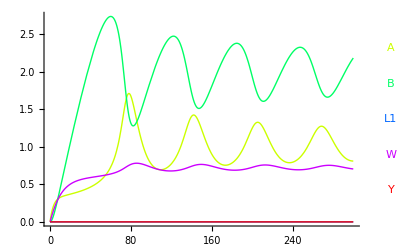

{{A→InterpolatingFunction[{{0.,300.}},<>],B→InterpolatingFunction[{{0.,300.}},<>],L1→InterpolatingFunction[{{0.,300.}},<>],W→InterpolatingFunction[{{0.,300.}},<>],Y→InterpolatingFunction[{{0.,300.}},<>]}}

```mathematica
s=run[circuit, timeSpan-> 300, rates-> parms, initialConditions-> {}, plot-> True]
```

Save the file to XML

```mathematica
SaveModel["WUS.xml", circuit, "Parameters"-> parms, "Description"-> "Wuschel Model Reactions from Jonsson et al (2005) Bioinformatics 21(S1):i232-i240" ]
```

Now read the XML and do another simulation

```mathematica
{anotherCircuit,anotherSetOfParameters, anoterSetOfic, opts} = GetModel["WUS.xml"]
```

Model: Model1

CelleratorML Version: 1.0

9 reactions

16 parameters

0 initial values

{{{Y↦W,GRN[1/tauw,Twy,1,hw,sigma]},{A↦W,GRN[1/tauw,Twa,1,hw,sigma]},{W→∅,dw},{L1→L1+Y,ky},{Y→∅,dy},{A+Y→Y,d},{∅⇄A,a,beta},{2 A+B→3 A,c},{A→B,b}},{ky→0.2,dy→0.1,Dy→0.1,kD→3.,tauw→10,dw→0.1,hw→0,Twy→-20,Twa→0.5,a→0.1,b→0.2,beta→0.1,c→0.1,d→0.01,Da→0.1,Db→1.5},{},{Name→Model1,Frozen→{}}}

```mathematica
run[anotherCircuit, timeSpan-> 300, rates-> anotherSetOfParameters, initialConditions-> anoterSetOfic, plot-> True]
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {A,B,L1,W,Y}

-Graphics-

{{A→InterpolatingFunction[{{0.,300.}},<>],B→InterpolatingFunction[{{0.,300.}},<>],L1→InterpolatingFunction[{{0.,300.}},<>],W→InterpolatingFunction[{{0.,300.}},<>],Y→InterpolatingFunction[{{0.,300.}},<>]}}

## Generate A Cellzilla Template from Random Geometry

This is a toy version, so it only uses 12 cells

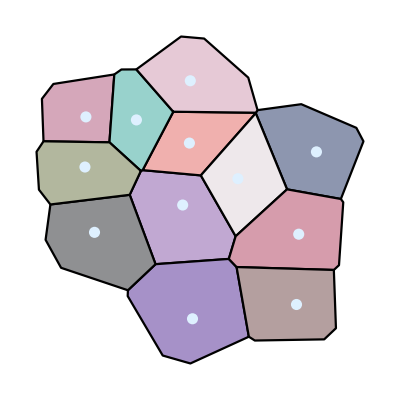

```mathematica
n=12; 
r:= RandomReal[{0, 100}]; 
centers=Table[{r,r}, {n}];
rc:= RandomReal[{0, 0.3}]; 
rcs=Table[CMYKColor[rc, rc, rc, rc], {n}];
sc=surfaceLayer[centers];
visualization[centers, cellColors-> rcs, Epilog-> {PointSize[.02], LightBlue, Point/@centers}]
```

```mathematica
centers
```

{{7.34192,85.5784},{40.1577,52.8309},{43.4901,10.5558},{85.5227,72.5843},{42.4401,75.8517},{24.472,84.4568},{42.7434,99.0107},{58.8851,62.6038},{10.2595,42.6769},{79.511,41.9866},{7.0187,66.9518},{78.6637,16.206}}

```mathematica
Export["template.pdf", visualization[centers, cellNumbers-> True, cellColors-> rcs, BaseStyle-> {FontSize-> 18}, Epilog-> {PointSize[.02], LightBlue, Point/@centers}]]
```

template.pdf

## Generate, Test, and Save a Cellzilla Model into XML with this Template

```mathematica
diffusingSpecies={{Y,Dy},{A,Da},{B,Db}};
```

```mathematica
rval:= RandomReal[{0, 1}]; 
rassign[sp_]:= sp-> 0;
rassign[sp_, num_]:= (rassign[sp[#]])&/@Range[num];
ric[sp_]:= rassign[sp, n];
L1IC=(L1[#]->If[MemberQ[sc,#],1,0])&/@Range[n];
theIC=Join[ric[W], ric[Y], ric[A], ric[B],L1IC];
```

```mathematica
theIC
```

{W[1]→0,W[2]→0,W[3]→0,W[4]→0,W[5]→0,W[6]→0,W[7]→0,W[8]→0,W[9]→0,W[10]→0,W[11]→0,W[12]→0,Y[1]→0,Y[2]→0,Y[3]→0,Y[4]→0,Y[5]→0,Y[6]→0,Y[7]→0,Y[8]→0,Y[9]→0,Y[10]→0,Y[11]→0,Y[12]→0,A[1]→0,A[2]→0,A[3]→0,A[4]→0,A[5]→0,A[6]→0,A[7]→0,A[8]→0,A[9]→0,A[10]→0,A[11]→0,A[12]→0,B[1]→0,B[2]→0,B[3]→0,B[4]→0,B[5]→0,B[6]→0,B[7]→0,B[8]→0,B[9]→0,B[10]→0,B[11]→0,B[12]→0,L1[1]→1,L1[2]→0,L1[3]→1,L1[4]→1,L1[5]→0,L1[6]→1,L1[7]→1,L1[8]→0,L1[9]→1,L1[10]→1,L1[11]→1,L1[12]→1}

Verify that the model works with Cellzilla

```mathematica
sys=GenerateSystem[centers,circuit,diffusingSpecies,{i,j}];
```

Generating reactions ...

Using Pruned Delaunay Triangulation for Near Neighbors Connections.

2 dimensional data

12 cells

108 internal reactions

144 intercellular reactions

0 global reactions

252 total reactions

0.124008 seconds CPU to generate network.

Generating differential equations ...

60 differential equations.

0.260016 seconds CPU to convert network to ODES.

```mathematica
sim=run[sys,{0,500},rates->parms,initialConditions->theIC, plot-> False];
```

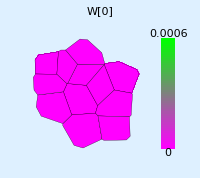

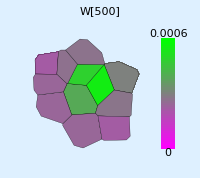

```mathematica
movieframes=animation[sim,{W,0, .0006},{0,500,500},cellCoordinates->centers,RGBColors->{{1,0,1},{0,1,0}},cellNumbers->False,wallThickness->0.001,Background->LightBlue,ImageSize->200,TextStyle->{FontFamily->Times,FontSize->32}];
```

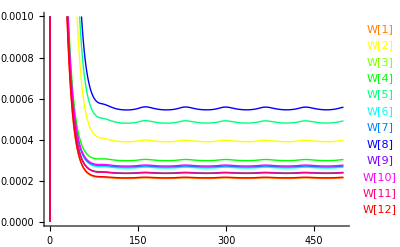

```mathematica
runPlot[sim, W/@Range[n], PlotRange-> {0, .001}]
```

## Save the CellzillaML File

```mathematica
SaveCellzillaModel["Wuschel-12-Cells.xml", "Models"-> {"WUS.xml"}, 
"Name"-> "Wuschel⎵Model⎵12⎵Cells", 
"Centers"-> centers, "Parameters"-> parms,"DiffusingSpecies"-> diffusingSpecies, "InitialConditions"-> theIC]
```

Model name: Wuschel⎵Model⎵12⎵Cells

Model file name(s) or URL(s):

WUS.xml

12 cell centers.

3 Diffusing Species

16 Parameters

60 Initial Conditions

Wuschel-12-Cells.xml

## Import the CellzillaML and run the simulation on it

```mathematica
importedModel=GetCellzillaModel["Wuschel-12-Cells.xml", "Quiet"-> True]
```

{Circuit→{{Y↦W,GRN[1/tauw,Twy,1,hw,sigma]},{A↦W,GRN[1/tauw,Twa,1,hw,sigma]},{W→∅,dw},{L1→L1+Y,ky},{Y→∅,dy},{A+Y→Y,d},{∅⇄A,a,beta},{2 A+B→3 A,c},{A→B,b}},Parameters→{a→0.1,b→0.2,beta→0.1,c→0.1,d→0.01,Da→0.1,Db→1.5,dw→0.1,dy→0.1,Dy→0.1,hw→0,kD→3.,ky→0.2,tauw→10,Twa→0.5,Twy→-20},IC→{A→{0,0,0,0,0,0,0,0,0,0,0,0},B→{0,0,0,0,0,0,0,0,0,0,0,0},L1→{1,0,1,1,0,1,1,0,1,1,1,1},W→{0,0,0,0,0,0,0,0,0,0,0,0},Y→{0,0,0,0,0,0,0,0,0,0,0,0}},DiffusingSpecies→{{Y,Dy},{A,Da},{B,Db}},Centers→{{7.34192,85.5784},{40.1577,52.8309},{43.4901,10.5558},{85.5227,72.5843},{42.4401,75.8517},{24.472,84.4568},{42.7434,99.0107},{58.8851,62.6038},{10.2595,42.6769},{79.511,41.9866},{7.0187,66.9518},{78.6637,16.206}}}

```mathematica
sys2=GenerateSystem[
"Centers"/.importedModel,
"Circuit"/.importedModel,
"DiffusingSpecies"/.importedModel,{i,j}];
```

Generating reactions ...

Using Pruned Delaunay Triangulation for Near Neighbors Connections.

2 dimensional data

12 cells

108 internal reactions

144 intercellular reactions

0 global reactions

252 total reactions

0.124008 seconds CPU to generate network.

Generating differential equations ...

60 differential equations.

0.256016 seconds CPU to convert network to ODES.

```mathematica
sim2=run[sys2,{0,500},rates->"Parameters"/.importedModel,
initialConditions->ListICToCellzillaIC["IC"/.importedModel]];
```

```mathematica
secondSetOFmovieframes=animation[sim2,{W,0, .0006},{0,500,500},
cellCoordinates->"Centers"/.importedModel,
RGBColors->{{1,0,1},{0,1,0}},cellNumbers->False,wallThickness->0.001,Background->LightBlue,ImageSize->200,TextStyle->{FontFamily->Times,FontSize->32}];
```

-Graphics-

-Graphics-